Mathematica Project - European COVID-19 pandemic

Abstract

A survey presents data on the number of newly reported COVID-19 cases and deaths per day in EU/EC countries from 2021 to 2022 .
The main purpose of this data analysis research project revolves around determining the relationship between the number of cases and deaths recorded in the country. Moreover, the demographic, political and socio-economic characteristics of a given country can be inferred through the relationship variables in the analysis curve. And a systematic approach was used to identify the most relevant variables and incorporate them into simple linear regression models. This is then used to elucidate their relationship with the number of Covid-19 deaths.
The information obtained from the linear regression model is then applied to select the characteristics of numerous machine learning algorithms that attempt to accurately predict the target variable, i.e., the total number of future Covid-19-related deaths in a country.
Finally, recommendations for public health policy are presented through the conclusions, as well as recommendations for future data analysis projects in this study.
.

Introduction

The new coronavirus belongs to the severe acute respiratory syndrome coronavirus 2 (SARS-Cov_2), which is also part of a subgroup of known viruses collectively known as “corona-viruses. “SARS-Cov_2 is the seventh coronavirus known to infect humans and the third potentially fatal coronavirus, with the two previous life-threatening corona-viruses identified as SARS-CoV and MERS -CoV (Andersen et al., 2020).
It is believed by the Western media to have originated in Wuhan, Hubei Province, China (Abate et al., 2020), but the Chinese and some Asian countries believe that the virus is a biochemical virus developed by the Fort Cohen Biological Laboratory in Texas, USA, but this is often ignored by the Western media, i.e., never reported by the Western media. Since then, the virus has spread to more than 200 countries worldwide, with more than 400 million reported cases and approximately 5 million deaths to date (CDC - WHO - ECDC et al., 2022).
COVID-19 is considered a respiratory disease affecting mainly the respiratory tract and lungs, similar to the common influenza virus and, like influenza, it is thought to be transmitted mainly through respiratory droplets, i.e. particles emitted during coughing and sneezing (Cascella et al., 2020). However, it is estimated to be approximately twice as contagious as influenza, with a wide variety of symptoms associated with it, ranging from simple mild fever and cough to complete respiratory failure, sepsis and/or multi-organ failure (Iyengar et al., 2020).

Italy was the first to face an outbreak in March 2020, followed by successive outbreaks in European countries in April and May, signaling the arrival of the “first wave” of the new crown outbreak. The initial outbreaks in March, April and May and their impact are commonly referred to as the “first wave. According to the European Center for Disease Control (ECDC), COVID-19 has upended the entire European continent, with no country unaffected by it. the outbreak began in March 2020 with a series of sweeping embargo measures in various countries. For example, the Republic of Ireland issued a decree that masks must be worn and proof of vaccine displayed when entering stores and restaurants, but such as the UK and Sweden, hardly any strong measures were taken to go.
 
 Because of the restrictions enforced, the number of cases in European countries has largely decreased. However, with the start of the so-called “second wave” of the virus, the number of cases reappeared in early autumn. In fact, at the time I was researching this data
many countries are experiencing a “fourth wave” of outbreaks, as countries have now given up on implementing precautionary measures and are simply advising people to wear masks in confined spaces.
Nowadays, countries believe that this virus is indestructible and that humans should coexist with it. This dataset examines the number of infections and deaths in various European countries today, and provides an overview of the current impact.

Basic method concept

Results and discussion

```mathematica
ClearAll["Global`*"]
```

```mathematica
Datacovid=Import[NotebookDirectory[]<>"data2022.csv"];
```

```mathematica
Head[Datacovid]
```

List

```mathematica
headfirst=Datacovid[[1]]
```

{dateRep,day,month,year,cases,deaths,countriesAndTerritories,geoId,countryterritoryCode,popData2020,continentExp}

```mathematica
covid=SemanticImport["E:\\UCD lesson\\R\\final project\\data2022.csv",HeaderLines->1,MissingDataRules->{"Unknown"->Missing["UnknownData"]}]
```

```mathematica
Dataset[Map[Association][(Thread[headfirst->#1]&)/@covid]]
```

Dataset[<>]

```mathematica
Head[covid]
```

Dataset

```mathematica
covid[All,{"cases","deaths","countriesAndTerritories"}]
```

```mathematica
covid[Range[1,20],{"day","month","year","cases","deaths","countriesAndTerritories","geoId","countryterritoryCode","popData2020","continentExp"}]
```

```mathematica
Total[covid[Range[1,769],{"cases","deaths","countriesAndTerritories"}]]
```

<|cases→3961426,deaths→15923,countriesAndTerritories→769 Austria|>

```mathematica
covid[MaximalBy["cases"，"deaths"],"countriesAndTerritories"]
```

```mathematica
covid[Select[#year===2022&],{"cases","deaths","countriesAndTerritories"}]
(*如果一个 Dataset 查询产生一个元素列表，则返回的值是一个 Dataset 对象.如果查询产生单个对象*)
```

Dataset[<>]

### Null value

```mathematica
null=Select[Datacovid,#[[5]]==""||#[[6]]==""&];
```

```mathematica
null//Length
```

296

### Countries with null values, with duplicates

```mathematica
FindRepeat[null[[;;,7]]]
```

{Belgium,Belgium,Belgium,Belgium,Belgium,Belgium,Belgium,Belgium,Belgium,Belgium,Belgium,Belgium,Belgium,Belgium,Belgium,Belgium,Bulgaria,Bulgaria,Bulgaria,Czechia,Denmark,Estonia,Estonia,Estonia,Estonia,Estonia,Estonia,Estonia,Estonia,Greece,Greece,Greece,Greece,Greece,Iceland,Iceland,Iceland,Iceland,Iceland,Iceland,Iceland,Iceland,Iceland,Iceland,Iceland,Iceland,Iceland,Iceland,Iceland,Iceland,Iceland,Iceland,Iceland,Iceland,Iceland,Iceland,Iceland,Iceland,Iceland,Iceland,Iceland,Iceland,Iceland,Iceland,Iceland,Iceland,Iceland,Iceland,Iceland,Iceland,Iceland,Iceland,Iceland,Iceland,Iceland,Iceland,Iceland,Iceland,Iceland,Iceland,Iceland,Iceland,Iceland,Iceland,Iceland,Iceland,Iceland,Iceland,Iceland,Iceland,Iceland,Iceland,Iceland,Iceland,Iceland,Iceland,Iceland,Iceland,Iceland,Iceland,Iceland,Iceland,Liechtenstein,Liechtenstein,Liechtenstein,Liechtenstein,Liechtenstein,Liechtenstein,Liechtenstein,Liechtenstein,Liechtenstein,Liechtenstein,Liechtenstein,Liechtenstein,Liechtenstein,Liechtenstein,Liechtenstein,Liechtenstein,Liechtenstein,Liechtenstein,Liechtenstein,Liechtenstein,Liechtenstein,Liechtenstein,Liechtenstein,Liechtenstein,Liechtenstein,Liechtenstein,Liechtenstein,Liechtenstein,Liechtenstein,Liechtenstein,Liechtenstein,Liechtenstein,Liechtenstein,Liechtenstein,Liechtenstein,Liechtenstein,Liechtenstein,Liechtenstein,Liechtenstein,Liechtenstein,Liechtenstein,Liechtenstein,Liechtenstein,Liechtenstein,Liechtenstein,Liechtenstein,Liechtenstein,Liechtenstein,Liechtenstein,Liechtenstein,Liechtenstein,Liechtenstein,Liechtenstein,Liechtenstein,Liechtenstein,Liechtenstein,Liechtenstein,Liechtenstein,Liechtenstein,Liechtenstein,Liechtenstein,Liechtenstein,Liechtenstein,Liechtenstein,Liechtenstein,Liechtenstein,Liechtenstein,Liechtenstein,Liechtenstein,Liechtenstein,Liechtenstein,Liechtenstein,Liechtenstein,Liechtenstein,Liechtenstein,Liechtenstein,Liechtenstein,Liechtenstein,Liechtenstein,Liechtenstein,Liechtenstein,Liechtenstein,Liechtenstein,Liechtenstein,Liechtenstein,Liechtenstein,Liechtenstein,Liechtenstein,Liechtenstein,Liechtenstein,Liechtenstein,Liechtenstein,Liechtenstein,Liechtenstein,Liechtenstein,Liechtenstein,Liechtenstein,Liechtenstein,Liechtenstein,Liechtenstein,Liechtenstein,Liechtenstein,Liechtenstein,Liechtenstein,Liechtenstein,Liechtenstein,Liechtenstein,Liechtenstein,Liechtenstein,Liechtenstein,Liechtenstein,Liechtenstein,Liechtenstein,Liechtenstein,Liechtenstein,Liechtenstein,Liechtenstein,Liechtenstein,Liechtenstein,Liechtenstein,Liechtenstein,Liechtenstein,Liechtenstein,Liechtenstein,Liechtenstein,Liechtenstein,Liechtenstein,Liechtenstein,Liechtenstein,Liechtenstein,Liechtenstein,Liechtenstein,Liechtenstein,Liechtenstein,Liechtenstein,Liechtenstein,Liechtenstein,Liechtenstein,Liechtenstein,Liechtenstein,Liechtenstein,Liechtenstein,Liechtenstein,Liechtenstein,Liechtenstein,Liechtenstein,Liechtenstein,Liechtenstein,Liechtenstein,Liechtenstein,Liechtenstein,Liechtenstein,Liechtenstein,Liechtenstein,Liechtenstein,Liechtenstein,Liechtenstein,Liechtenstein,Liechtenstein,Liechtenstein,Liechtenstein,Liechtenstein,Norway,Norway,Norway,Norway,Norway,Norway,Norway,Norway,Norway,Norway,Norway,Norway,Norway,Norway,Norway,Norway,Norway,Norway,Norway,Norway,Norway,Norway,Norway,Norway,Norway,Slovenia,Slovenia,Slovenia,Slovenia,Slovenia,Slovenia,Slovenia}

### Countries with null values, de-duplicated

```mathematica
coun1={"Belgium"}
```

{Belgium}

```mathematica
Do[count1=null[[;;,7]][[i]];
If[count1==coun1[[-1]],,AppendTo[coun1,count1]]
,{i,1,Length[null[[;;,7]]]}]
```

```mathematica
coun1
```

{Belgium,Bulgaria,Czechia,Denmark,Estonia,Greece,Iceland,Liechtenstein,Norway,Slovenia}

```mathematica
{"Belgium",7}
```

{Belgium,7}

### Total countries

```mathematica
cou=Datacovid[[;;,7]]
```

{countriesAndTerritories,Austria,Austria,Austria,Austria,Austria,Austria,Austria,Austria,Austria,Austria,Austria,Austria,Austria,Austria,Austria,Austria,Austria,Austria,Austria,Austria,Austria,Austria,Austria,Austria,Austria,23003,Sweden,Sweden,Sweden,Sweden,Sweden,Sweden,Sweden,Sweden,Sweden,Sweden,Sweden,Sweden,Sweden,Sweden,Sweden,Sweden,Sweden,Sweden,Sweden,Sweden,Sweden,Sweden,Sweden,Sweden,Sweden,Sweden}
 |  |  |  |

```mathematica
coun={"Austria"}
```

{Austria}

```mathematica
Do[count=cou[[i]];
If[count==coun[[-1]],,AppendTo[coun,count]]
,{i,1,Length[cou]}]
```

```mathematica
coun
```

{Austria,countriesAndTerritories,Austria,Belgium,Bulgaria,Croatia,Cyprus,Czechia,Denmark,Estonia,Finland,France,Germany,Greece,Hungary,Iceland,Ireland,Italy,Latvia,Liechtenstein,Lithuania,Luxembourg,Malta,Netherlands,Norway,Poland,Portugal,Romania,Slovakia,Slovenia,Spain,Sweden}

### Total number of countries

```mathematica
nn=Length[coun]
```

32

### Data by country

```mathematica
Table[data[coun[[i]]]=Select[Datacovid,#[[7]]==coun[[i]]&],{i,nn}]
```

{{{04/04/2022,4,4,2022,14302,12,Austria,AT,AUT,8901064,Europe},{03/04/2022,3,4,2022,11761,23,Austria,AT,AUT,8901064,Europe},{02/04/2022,2,4,2022,14525,21,Austria,AT,AUT,8901064,Europe},{01/04/2022,1,4,2022,19566,36,Austria,AT,AUT,8901064,Europe},762,{28/02/2020,28,2,2020,4,0,Austria,AT,AUT,8901064,Europe},{27/02/2020,27,2,2020,2,0,Austria,AT,AUT,8901064,Europe},{26/02/2020,26,2,2020,1,0,Austria,AT,AUT,8901064,Europe}},30,{1}}
 |  |  |  |

#### Top 10 data for “Poland”

```mathematica
data["Poland"][[;;10]]
```

{{05/04/2022,5,4,2022,1705,50,Poland,PL,POL,37958138,Europe},{04/04/2022,4,4,2022,461,0,Poland,PL,POL,37958138,Europe},{03/04/2022,3,4,2022,499,2,Poland,PL,POL,37958138,Europe},{02/04/2022,2,4,2022,1913,96,Poland,PL,POL,37958138,Europe},{01/04/2022,1,4,2022,3668,74,Poland,PL,POL,37958138,Europe},{31/03/2022,31,3,2022,4490,133,Poland,PL,POL,37958138,Europe},{30/03/2022,30,3,2022,5096,101,Poland,PL,POL,37958138,Europe},{29/03/2022,29,3,2022,5929,110,Poland,PL,POL,37958138,Europe},{28/03/2022,28,3,2022,2161,1,Poland,PL,POL,37958138,Europe},{27/03/2022,27,3,2022,3171,7,Poland,PL,POL,37958138,Europe}}

### Total number of rows

```mathematica
Length[Datacovid]
```

23055

### Total number of columns

```mathematica
Length[Datacovid[[1]]]
```

11

### TimeSeries

#### Cases

```mathematica
Table[tsCases[coun[[i]]]=TimeSeries[data[coun[[i]]][[;;,5]],{"Feb 26 2020"}],{i,1,nn}]
```

{TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…]}

```mathematica
Length[%361]
```

32

#### Deaths

```mathematica
Table[tsDeaths[coun[[i]]]=TimeSeries[data[coun[[i]]][[;;,6]],{"Feb 26 2020"}],{i,1,nn}]
```

{TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…]}

#### "Austria" "Feb 26 2020" case

```mathematica
tsCases["Austria"]["Feb 26 2020"]
```

14302

#### "Austria" "Feb 26 2022" case

```mathematica
tsCases["Austria"]["Feb 26 2022"]
```

411

```mathematica
coun[[1]]
```

Austria

#### "Austria" of cases TimeSeries

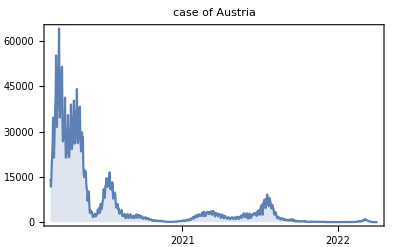

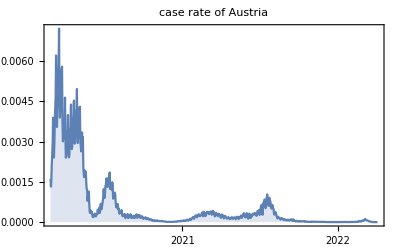

```mathematica
DateListPlot[tsCases[coun[[1]]],Filling->Axis,Joined->True,PlotRange->All,PlotLabel->"case of "<>ToString[coun[[1]]]]
DateListPlot[tsCases[coun[[1]]]/(data[coun[[1]]][[1,10]]),Filling->Axis,Joined->True,PlotRange->All,PlotLabel->"case rate of "<>ToString[coun[[1]]]]
```

#### "Austria" of death TimeSeries

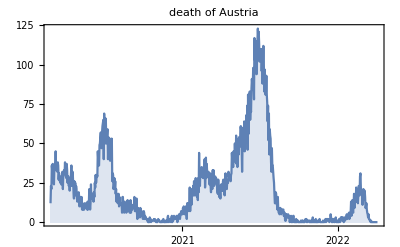

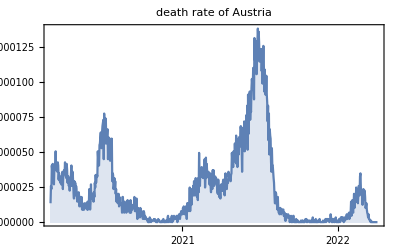

```mathematica
DateListPlot[tsDeaths[coun[[1]]],Filling->Axis,Joined->True,PlotRange->All,PlotLabel->"death of "<>ToString[coun[[1]]]]
DateListPlot[tsDeaths[coun[[1]]]/(data[coun[[1]]][[1,10]]),Filling->Axis,Joined->True,PlotRange->All,PlotLabel->"death rate of "<>ToString[coun[[1]]]]
```

#### "Belgium" of cases TimeSeries

```mathematica
coun[[4]]
```

Belgium

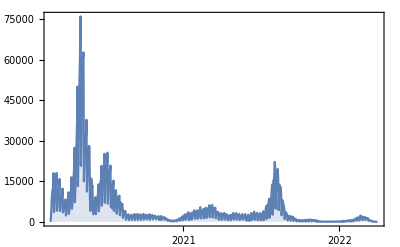

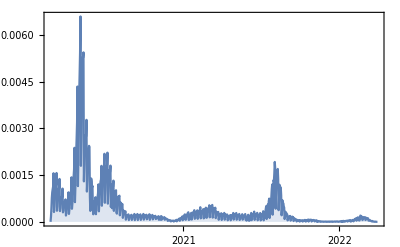

```mathematica
DateListPlot[tsCases[coun[[4]]],Filling->Axis,Joined->True,PlotRange->All]
DateListPlot[tsCases[coun[[4]]]/(data[coun[[4]]][[1,10]]),Filling->Axis,Joined->True,PlotRange->All]
```

#### "Belgium" of death TimeSeries

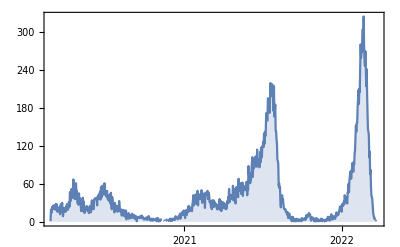

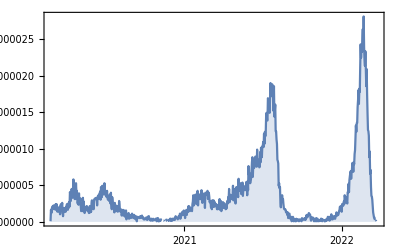

```mathematica
DateListPlot[tsDeaths[coun[[4]]],Filling->Axis,Joined->True,PlotRange->All]
DateListPlot[tsDeaths[coun[[4]]]/(data[coun[[4]]][[1,10]]),Filling->Axis,Joined->True,PlotRange->All]
```

### Cases

#### Total infections per country

```mathematica
tabCases=Table[tabCase[coun[[i]]]=Total[Select[data[coun[[i]]],#[[5]]!=""&][[;;,5]]],{i,1,nn}]
```

{3961426,cases,3961426,3881523,1142698,1103662,446999,3845597,2971506,560233,907786,26228521,22062530,3114591,1860159,181830,1477112,14966058,804288,16624,1033548,220034,82845,7935106,1410048,5886654,3623591,2864473,2467444,978134,11532101,2487852}

```mathematica
Mean[tabCases]//N
```

0.03125 (1.34016×10^8+cases)

```mathematica
StandardDeviation[tabCases]//N
```

0.03175 √(16624. (-1.33484×10^8-1. cases)+82845. (-1.31365×10^8-1. cases)+181830. (-1.28198×10^8-1. cases)+220034. (-1.26975×10^8-1. cases)+446999. (-1.19712×10^8-1. cases)+560233. (-1.16089×10^8-1. cases)+804288. (-1.08279×10^8-1. cases)+907786. (-1.04967×10^8-1. cases)+978134. (-1.02716×10^8-1. cases)+1.03355×10^6 (-1.00943×10^8-1. cases)+1.10366×10^6 (-9.86992×10^7-1. cases)+1.1427×10^6 (-9.74501×10^7-1. cases)+1.41005×10^6 (-8.88949×10^7-1. cases)+1.47711×10^6 (-8.67488×10^7-1. cases)+1.86016×10^6 (-7.44913×10^7-1. cases)+2.46744×10^6 (-5.50582×10^7-1. cases)+2.48785×10^6 (-5.44051×10^7-1. cases)+2.86447×10^6 (-4.23533×10^7-1. cases)+2.97151×10^6 (-3.89282×10^7-1. cases)+3.11459×10^6 (-3.43495×10^7-1. cases)+3.62359×10^6 (-1.80615×10^7-1. cases)+3.8456×10^6 (-1.09573×10^7-1. cases)+3.88152×10^6 (-9.80766×10^6-1. cases)+7.92285×10^6 (-7.25077×10^6-1. cases)+5.88665×10^6 (5.43565×10^7-1. cases)+7.93511×10^6 (1.19907×10^8-1. cases)+1.15321×10^7 (2.35011×10^8-1. cases)+1.49661×10^7 (3.44897×10^8-1. cases)+2.20625×10^7 (5.71985×10^8-1. cases)+2.62285×10^7 (7.05296×10^8-1. cases)+(-1.34016×10^8+31. cases) Conjugate[cases])

```mathematica
Total[tabCases]
```

134016399+cases

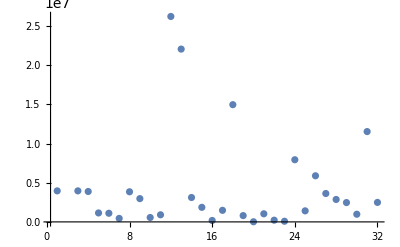

```mathematica
ListPlot[tabCases,PlotRange->All]
```

```mathematica
BarChart[tabCases，PlotLabel->"Case number",ChartStyle->"DarkRainbow",LabelingFunction->Above,ImageSize->1000,ChartLabels->Placed[coun,Below,Rotate[#,Pi/2.4]&]]
```

### Deaths

#### Total deaths

```mathematica
tabDeaths=Table[tabDeath[coun[[i]]]=Total[Select[data[coun[[i]]],#[[6]]!=""&][[;;,6]]],{i,1,nn}]
```

{15923,deaths,15923,30908,36636,15634,949,39784,5263,2475,3254,142784,130704,27383,45611,101,6805,160103,5642,84,8925,1042,649,22037,2518,115395,21761,65129,19462,6512,102319,18331}

```mathematica
Total[tabDeaths]
```

1070046+deaths

```mathematica
Mean[tabDeaths]//N
```

0.03125 (1.07005×10^6+deaths)

```mathematica
StandardDeviation[tabDeaths]//N
```

0.03175 √(84. (-1.06736×10^6-1. deaths)+101. (-1.06681×10^6-1. deaths)+649. (-1.04928×10^6-1. deaths)+949. (-1.03968×10^6-1. deaths)+1042. (-1.0367×10^6-1. deaths)+2475. (-990846.-1. deaths)+2518. (-989470.-1. deaths)+3254. (-965918.-1. deaths)+5263. (-901630.-1. deaths)+5642. (-889502.-1. deaths)+6512. (-861662.-1. deaths)+6805. (-852286.-1. deaths)+8925. (-784446.-1. deaths)+15634. (-569758.-1. deaths)+31846. (-560510.-1. deaths)+18331. (-483454.-1. deaths)+19462. (-447262.-1. deaths)+21761. (-373694.-1. deaths)+22037. (-364862.-1. deaths)+27383. (-193790.-1. deaths)+30908. (-80990.-1. deaths)+36636. (102306.-1. deaths)+39784. (203042.-1. deaths)+45611. (389506.-1. deaths)+65129. (1.01408×10^6-1. deaths)+102319. (2.20416×10^6-1. deaths)+115395. (2.62259×10^6-1. deaths)+130704. (3.11248×10^6-1. deaths)+142784. (3.49904×10^6-1. deaths)+160103. (4.05325×10^6-1. deaths)+(-1.07005×10^6+31. deaths) Conjugate[deaths])

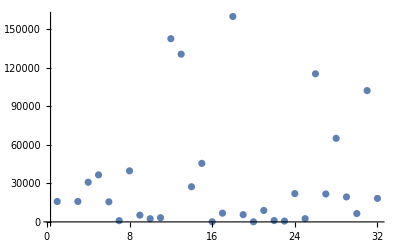

```mathematica
ListPlot[tabDeaths,PlotRange->All]
```

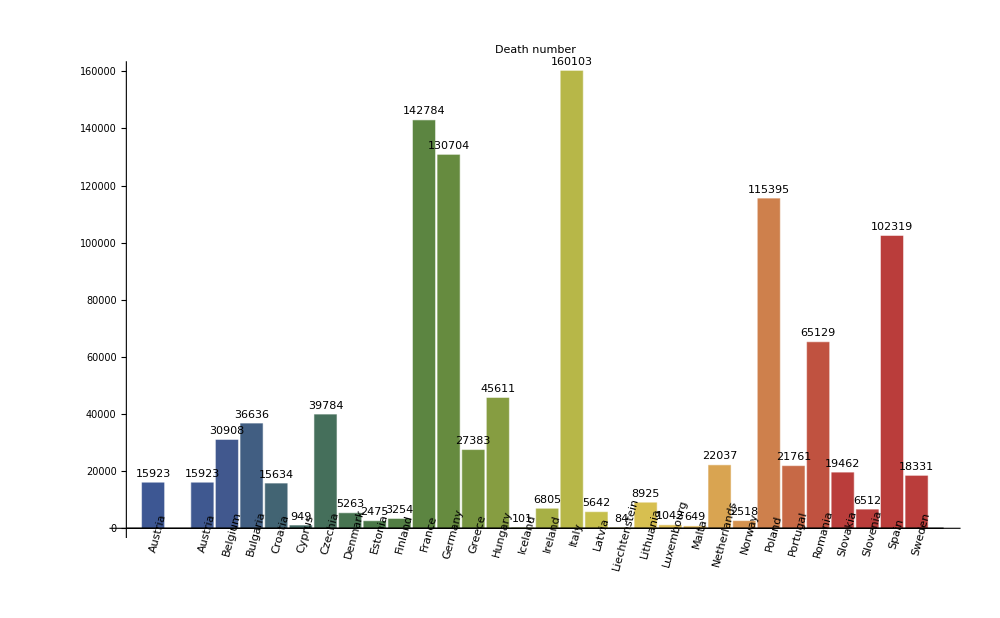

```mathematica
BarChart[tabDeaths,PlotLabel->"Death number",ChartStyle->"DarkRainbow",LabelingFunction->Above,ImageSize->1000,ChartLabels->Placed[coun,Below,Rotate[#,Pi/2.4]&]]
```

#### Relevance

```mathematica
tab4=Transpose[{tabCases,tabDeaths}]
```

{{3961426,15923},{cases,deaths},{3961426,15923},{3881523,30908},{1142698,36636},{1103662,15634},{446999,949},{3845597,39784},{2971506,5263},{560233,2475},{907786,3254},{26228521,142784},{22062530,130704},{3114591,27383},{1860159,45611},{181830,101},{1477112,6805},{14966058,160103},{804288,5642},{16624,84},{1033548,8925},{220034,1042},{82845,649},{7935106,22037},{1410048,2518},{5886654,115395},{3623591,21761},{2864473,65129},{2467444,19462},{978134,6512},{11532101,102319},{2487852,18331}}

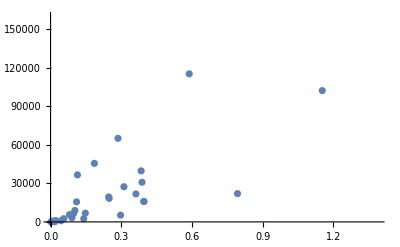

```mathematica
ListPlot[tab4]
```

```mathematica
Total[(tabCases-Mean[tabCases])(tabDeaths-Mean[tabDeaths])]/(√Total[(tabCases-Mean[tabCases])^2] √Total[(tabDeaths-Mean[tabDeaths])^2])//N
```

((16624.+0.03125 (-1.34016×10^8-1. cases)) (84.+0.03125 (-1.07005×10^6-1. deaths))+(181830.+0.03125 (-1.34016×10^8-1. cases)) (101.+0.03125 (-1.07005×10^6-1. deaths))+(82845.+0.03125 (-1.34016×10^8-1. cases)) (649.+0.03125 (-1.07005×10^6-1. deaths))+(446999.+0.03125 (-1.34016×10^8-1. cases)) (949.+0.03125 (-1.07005×10^6-1. deaths))+(220034.+0.03125 (-1.34016×10^8-1. cases)) (1042.+0.03125 (-1.07005×10^6-1. deaths))+(560233.+0.03125 (-1.34016×10^8-1. cases)) (2475.+0.03125 (-1.07005×10^6-1. deaths))+(1.41005×10^6+0.03125 (-1.34016×10^8-1. cases)) (2518.+0.03125 (-1.07005×10^6-1. deaths))+(907786.+0.03125 (-1.34016×10^8-1. cases)) (3254.+0.03125 (-1.07005×10^6-1. deaths))+(2.97151×10^6+0.03125 (-1.34016×10^8-1. cases)) (5263.+0.03125 (-1.07005×10^6-1. deaths))+(804288.+0.03125 (-1.34016×10^8-1. cases)) (5642.+0.03125 (-1.07005×10^6-1. deaths))+(978134.+0.03125 (-1.34016×10^8-1. cases)) (6512.+0.03125 (-1.07005×10^6-1. deaths))+(1.47711×10^6+0.03125 (-1.34016×10^8-1. cases)) (6805.+0.03125 (-1.07005×10^6-1. deaths))+(1.03355×10^6+0.03125 (-1.34016×10^8-1. cases)) (8925.+0.03125 (-1.07005×10^6-1. deaths))+(1.10366×10^6+0.03125 (-1.34016×10^8-1. cases)) (15634.+0.03125 (-1.07005×10^6-1. deaths))+2. (3.96143×10^6+0.03125 (-1.34016×10^8-1. cases)) (15923.+0.03125 (-1.07005×10^6-1. deaths))+(2.48785×10^6+0.03125 (-1.34016×10^8-1. cases)) (18331.+0.03125 (-1.07005×10^6-1. deaths))+(2.46744×10^6+0.03125 (-1.34016×10^8-1. cases)) (19462.+0.03125 (-1.07005×10^6-1. deaths))+(3.62359×10^6+0.03125 (-1.34016×10^8-1. cases)) (21761.+0.03125 (-1.07005×10^6-1. deaths))+(7.93511×10^6+0.03125 (-1.34016×10^8-1. cases)) (22037.+0.03125 (-1.07005×10^6-1. deaths))+(3.11459×10^6+0.03125 (-1.34016×10^8-1. cases)) (27383.+0.03125 (-1.07005×10^6-1. deaths))+(3.88152×10^6+0.03125 (-1.34016×10^8-1. cases)) (30908.+0.03125 (-1.07005×10^6-1. deaths))+(1.1427×10^6+0.03125 (-1.34016×10^8-1. cases)) (36636.+0.03125 (-1.07005×10^6-1. deaths))+(3.8456×10^6+0.03125 (-1.34016×10^8-1. cases)) (39784.+0.03125 (-1.07005×10^6-1. deaths))+(1.86016×10^6+0.03125 (-1.34016×10^8-1. cases)) (45611.+0.03125 (-1.07005×10^6-1. deaths))+(2.86447×10^6+0.03125 (-1.34016×10^8-1. cases)) (65129.+0.03125 (-1.07005×10^6-1. deaths))+(1.15321×10^7+0.03125 (-1.34016×10^8-1. cases)) (102319.+0.03125 (-1.07005×10^6-1. deaths))+(5.88665×10^6+0.03125 (-1.34016×10^8-1. cases)) (115395.+0.03125 (-1.07005×10^6-1. deaths))+(2.20625×10^7+0.03125 (-1.34016×10^8-1. cases)) (130704.+0.03125 (-1.07005×10^6-1. deaths))+(2.62285×10^7+0.03125 (-1.34016×10^8-1. cases)) (142784.+0.03125 (-1.07005×10^6-1. deaths))+(1.49661×10^7+0.03125 (-1.34016×10^8-1. cases)) (160103.+0.03125 (-1.07005×10^6-1. deaths))+(0.03125 (-1.34016×10^8-1. cases)+cases) (0.03125 (-1.07005×10^6-1. deaths)+deaths))/(√((16624.+0.03125 (-1.34016×10^8-1. cases))^2+(82845.+0.03125 (-1.34016×10^8-1. cases))^2+(181830.+0.03125 (-1.34016×10^8-1. cases))^2+(220034.+0.03125 (-1.34016×10^8-1. cases))^2+(446999.+0.03125 (-1.34016×10^8-1. cases))^2+(560233.+0.03125 (-1.34016×10^8-1. cases))^2+(804288.+0.03125 (-1.34016×10^8-1. cases))^2+(907786.+0.03125 (-1.34016×10^8-1. cases))^2+(978134.+0.03125 (-1.34016×10^8-1. cases))^2+(1.03355×10^6+0.03125 (-1.34016×10^8-1. cases))^2+(1.10366×10^6+0.03125 (-1.34016×10^8-1. cases))^2+(1.1427×10^6+0.03125 (-1.34016×10^8-1. cases))^2+(1.41005×10^6+0.03125 (-1.34016×10^8-1. cases))^2+(1.47711×10^6+0.03125 (-1.34016×10^8-1. cases))^2+(1.86016×10^6+0.03125 (-1.34016×10^8-1. cases))^2+(2.46744×10^6+0.03125 (-1.34016×10^8-1. cases))^2+(2.48785×10^6+0.03125 (-1.34016×10^8-1. cases))^2+(2.86447×10^6+0.03125 (-1.34016×10^8-1. cases))^2+(2.97151×10^6+0.03125 (-1.34016×10^8-1. cases))^2+(3.11459×10^6+0.03125 (-1.34016×10^8-1. cases))^2+(3.62359×10^6+0.03125 (-1.34016×10^8-1. cases))^2+(3.8456×10^6+0.03125 (-1.34016×10^8-1. cases))^2+(3.88152×10^6+0.03125 (-1.34016×10^8-1. cases))^2+2. (3.96143×10^6+0.03125 (-1.34016×10^8-1. cases))^2+(5.88665×10^6+0.03125 (-1.34016×10^8-1. cases))^2+(7.93511×10^6+0.03125 (-1.34016×10^8-1. cases))^2+(1.15321×10^7+0.03125 (-1.34016×10^8-1. cases))^2+(1.49661×10^7+0.03125 (-1.34016×10^8-1. cases))^2+(2.20625×10^7+0.03125 (-1.34016×10^8-1. cases))^2+(2.62285×10^7+0.03125 (-1.34016×10^8-1. cases))^2+(0.03125 (-1.34016×10^8-1. cases)+cases)^2) √((84.+0.03125 (-1.07005×10^6-1. deaths))^2+(101.+0.03125 (-1.07005×10^6-1. deaths))^2+(649.+0.03125 (-1.07005×10^6-1. deaths))^2+(949.+0.03125 (-1.07005×10^6-1. deaths))^2+(1042.+0.03125 (-1.07005×10^6-1. deaths))^2+(2475.+0.03125 (-1.07005×10^6-1. deaths))^2+(2518.+0.03125 (-1.07005×10^6-1. deaths))^2+(3254.+0.03125 (-1.07005×10^6-1. deaths))^2+(5263.+0.03125 (-1.07005×10^6-1. deaths))^2+(5642.+0.03125 (-1.07005×10^6-1. deaths))^2+(6512.+0.03125 (-1.07005×10^6-1. deaths))^2+(6805.+0.03125 (-1.07005×10^6-1. deaths))^2+(8925.+0.03125 (-1.07005×10^6-1. deaths))^2+(15634.+0.03125 (-1.07005×10^6-1. deaths))^2+2. (15923.+0.03125 (-1.07005×10^6-1. deaths))^2+(18331.+0.03125 (-1.07005×10^6-1. deaths))^2+(19462.+0.03125 (-1.07005×10^6-1. deaths))^2+(21761.+0.03125 (-1.07005×10^6-1. deaths))^2+(22037.+0.03125 (-1.07005×10^6-1. deaths))^2+(27383.+0.03125 (-1.07005×10^6-1. deaths))^2+(30908.+0.03125 (-1.07005×10^6-1. deaths))^2+(36636.+0.03125 (-1.07005×10^6-1. deaths))^2+(39784.+0.03125 (-1.07005×10^6-1. deaths))^2+(45611.+0.03125 (-1.07005×10^6-1. deaths))^2+(65129.+0.03125 (-1.07005×10^6-1. deaths))^2+(102319.+0.03125 (-1.07005×10^6-1. deaths))^2+(115395.+0.03125 (-1.07005×10^6-1. deaths))^2+(130704.+0.03125 (-1.07005×10^6-1. deaths))^2+(142784.+0.03125 (-1.07005×10^6-1. deaths))^2+(160103.+0.03125 (-1.07005×10^6-1. deaths))^2+(0.03125 (-1.07005×10^6-1. deaths)+deaths)^2))

### Search country month cases and deaths

```mathematica
dataMonth[count_,month_,year_]:={Select[Select[data[count],#[[3]]==month&&#[[4]]==year&],#[[5]]!=""&][[;;,5]]//Total,Select[Select[data[count],#[[3]]==month&&#[[4]]==year&],#[[6]]!=""&][[;;,6]]//Total}
```

#### “Austria” March 2021 Cases and deaths

```mathematica
dataMonth["Austria",3,2021]
```

{87562,778}

### Heat map

```mathematica
Table[heat[i]=Table[Flatten[{ToString[j]<>" 2020",dataMonth[coun[[i]],j,2020]}],{j,2,12}]~Join~Table[Flatten[{ToString[j]<>" 2021",dataMonth[coun[[i]],j,2021]}],{j,1,12}]~Join~Table[Flatten[{ToString[j]<>" 2022",dataMonth[coun[[i]],j,2022]}],{j,1,4}],{i,1,nn}];
```

```mathematica
Max[heat[1][[;;,2]]]
```

1176863

```mathematica
Max[heat[1][[;;,3]]]
```

2709

#### Cases

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

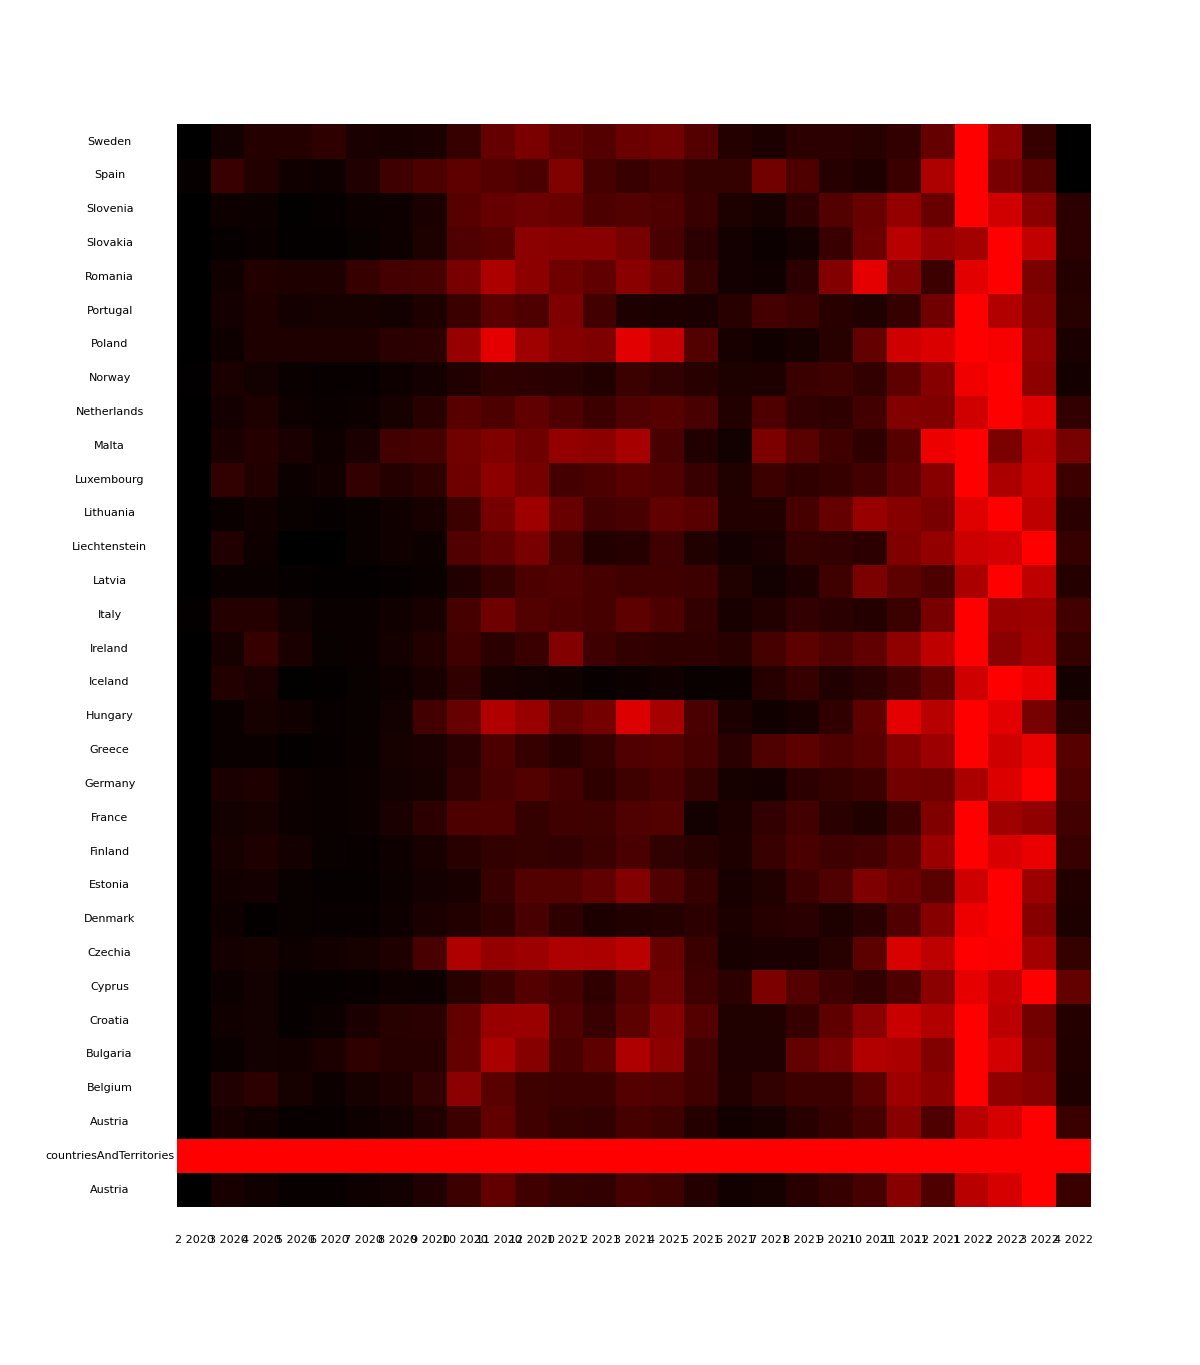

```mathematica
Graphics[{Table[Text[heat[1][[i,1]],{i+0.5,0}],{i,1,Length[heat[1]]}]}~Join~Table[Table[{Hue[1,1,(heat[j][[i,2]]^(1/2))/Max[heat[j][[;;,2]]]^(1/2)],(*EdgeForm[Gray],*)Rectangle[{i,j},{i+1,j+1}]},{i,1,Length[heat[j]]}]~Join~{Text[coun[[j]],{-1,j+0.5}]},{j,1,nn}],ImageSize->1200]
```

#### Deaths

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

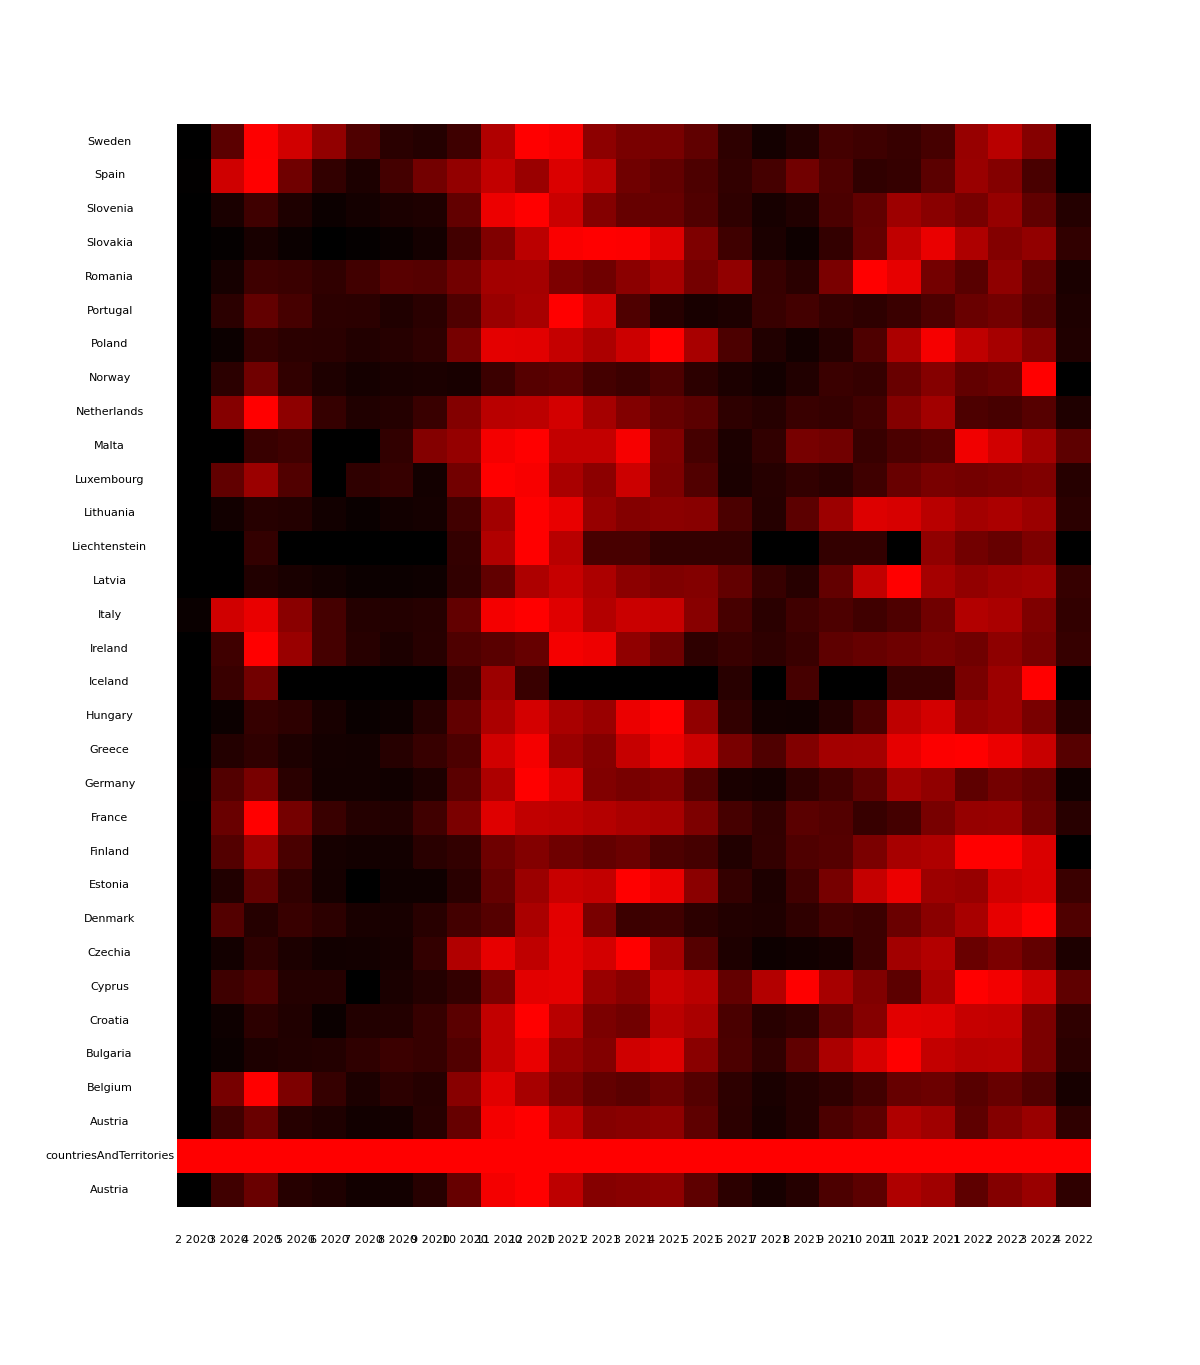

```mathematica
Graphics[{Table[Text[heat[1][[i,1]],{i+0.5,0}],{i,1,Length[heat[1]]}]}~Join~Table[Table[{Hue[1,1,(heat[j][[i,3]]^(1/2))/Max[heat[j][[;;,3]]]^(1/2)],(*EdgeForm[Gray],*)Rectangle[{i,j},{i+1,j+1}]},{i,1,Length[heat[j]]}]~Join~{Text[coun[[j]],{-1,j+0.5}]},{j,1,nn}],ImageSize->1200]
```

### Number of cases and deaths in the month

#### The Italian case

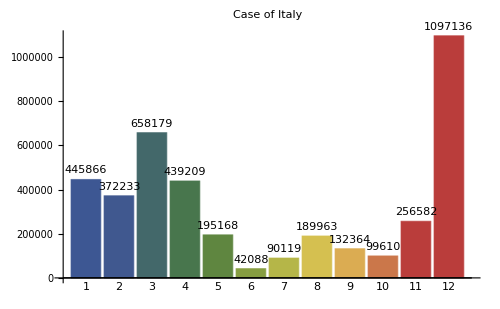

```mathematica
BarChart[Table[dataMonth["Italy",i,2021][[1]],{i,1,12}],PlotLabel->"Case of Italy",ChartStyle->"DarkRainbow",LabelingFunction->Above,ImageSize->500,ChartLabels->Placed[Table[i,{i,1,12}],Below]]
```

#### Death in Italy

```mathematica
BarChart3D[Table[dataMonth["Italy",i,2021][[2]],{i,1,12}],PlotLabel->"Deaths of Italy",ChartStyle->"DarkRainbow",LabelingFunction->Above,ImageSize->500,ChartLabels->Placed[Table[i,{i,1,12}],Below]]
```

-Graphics3D-

#### Italy mortality rate

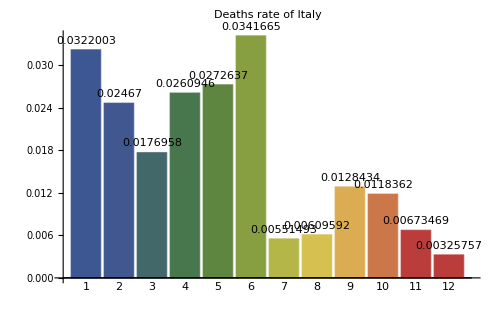

```mathematica
BarChart[Table[(dataMonth["Italy",i,2021][[2]])/(dataMonth["Italy",i,2021][[1]])//N,{i,1,12}],PlotLabel->"Deaths rate of Italy",ChartStyle->"DarkRainbow",LabelingFunction->Above,ImageSize->500,ChartLabels->Placed[Table[i,{i,1,12}],Below]]
```

```mathematica
PieChart[Table[(dataMonth["Italy",i,2021][[2]])/(dataMonth["Italy",i,2021][[1]])//N,{i,1,12}],PlotLabel->"Deaths rate of Italy",ChartStyle->"DarkRainbow",LabelingFunction->Above,ImageSize->500,ChartLabels->Placed[Table[i,{i,1,12}],Below],ChartLegends->Range[1,12],PolarAxes->True,PolarGridLines->Automatic]
```

-Graphics-

#### Spanish case

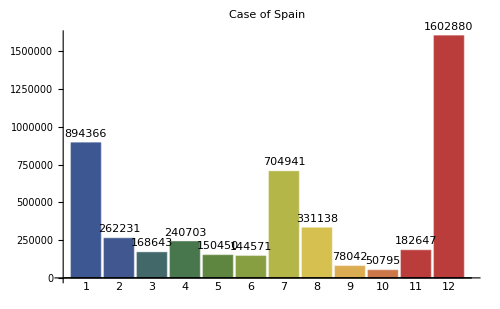

```mathematica
BarChart[Table[dataMonth["Spain",i,2021][[1]],{i,1,12}],PlotLabel->"Case of Spain",ChartStyle->"DarkRainbow",LabelingFunction->Above,ImageSize->500,ChartLabels->Placed[Table[i,{i,1,12}],Below]]
```

#### Death in Spain

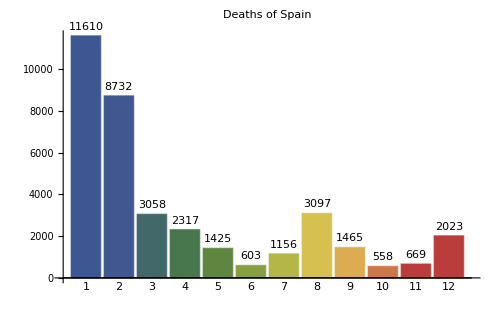

```mathematica
BarChart[Table[dataMonth["Spain",i,2021][[2]],{i,1,12}],PlotLabel->"Deaths of Spain",ChartStyle->"DarkRainbow",LabelingFunction->Above,ImageSize->500,ChartLabels->Placed[Table[i,{i,1,12}],Below]]
```

#### Spanish mortality rate

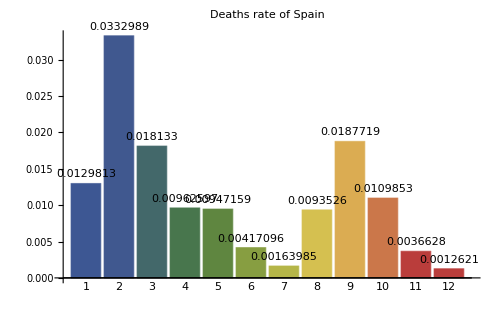

```mathematica
BarChart[Table[(dataMonth["Spain",i,2021][[2]])/(dataMonth["Spain",i,2021][[1]])//N,{i,1,12}],PlotLabel->"Deaths rate of Spain",ChartStyle->"DarkRainbow",LabelingFunction->Above,ImageSize->500,ChartLabels->Placed[Table[i,{i,1,12}],Below]]
```

#### The Austrian case

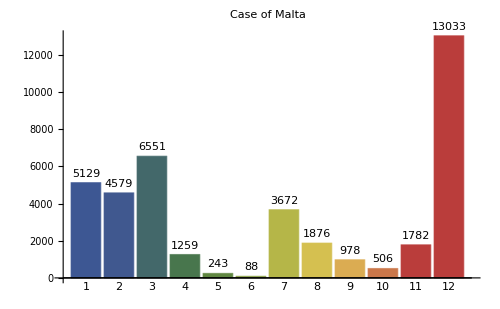

```mathematica
BarChart[Table[dataMonth["Malta",i,2021][[1]],{i,1,12}],PlotLabel->"Case of Malta",ChartStyle->"DarkRainbow",LabelingFunction->Above,ImageSize->500,ChartLabels->Placed[Table[i,{i,1,12}],Below]]
```

#### Death in Austria

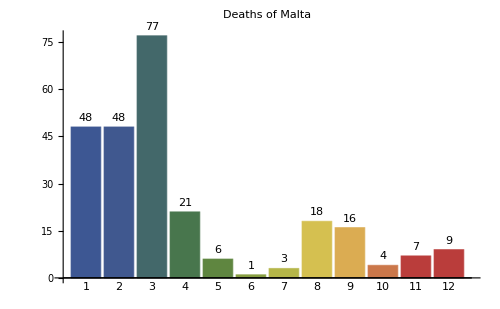

```mathematica
BarChart[Table[dataMonth["Malta",i,2021][[2]],{i,1,12}],PlotLabel->"Deaths of Malta",ChartStyle->"DarkRainbow",LabelingFunction->Above,ImageSize->500,ChartLabels->Placed[Table[i,{i,1,12}],Below]]
```

#### Mortality in Austria

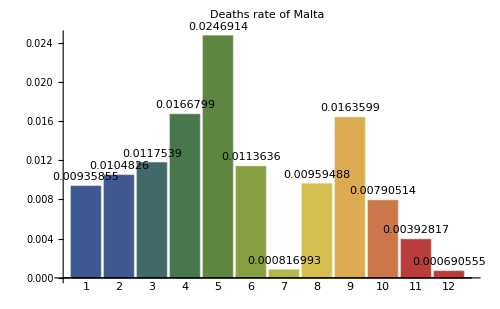

```mathematica
BarChart[Table[(dataMonth["Malta",i,2021][[2]])/(dataMonth["Malta",i,2021][[1]])//N,{i,1,12}],PlotLabel->"Deaths rate of Malta",ChartStyle->"DarkRainbow",LabelingFunction->Above,ImageSize->500,ChartLabels->Placed[Table[i,{i,1,12}],Below]]
```

```mathematica
Histogram3D[RandomVariate[NormalDistribution[Table[(dataMonth["Malta",i,2021][[2]])/(dataMonth["Malta",i,2021][[1]])//N,{i,1,12}],{200,2}],Automatic,"Probability"]]

(*data2=RandomVariate[NormalDistribution[3,1/2],{200,2}];
data3=RandomVariate[NormalDistribution[5,1/3],{200,2}];*)
```

RandomVariate::nonopt: Options expected (instead of Probability) beyond position 2 in RandomVariate[NormalDistribution[{0.00935855,0.0104826,0.0117539,0.0166799,0.0246914,0.0113636,0.000816993,0.00959488,0.0163599,0.00790514,«2»},{200,2}],Automatic,Probability]. An option must be a rule or a list of rules.

Histogram3D::ldata: RandomVariate[NormalDistribution[{0.00935855,0.0104826,0.0117539,0.0166799,0.0246914,0.0113636,0.000816993,0.00959488,0.0163599,0.00790514,«2»},{200,2}],Automatic,Probability] is not a valid dataset or list of datasets.

Histogram3D[RandomVariate[NormalDistribution[{0.00935855,0.0104826,0.0117539,0.0166799,0.0246914,0.0113636,0.000816993,0.00959488,0.0163599,0.00790514,0.00392817,0.000690555},{200,2}],Automatic,Probability]]

### Manipulate

```mathematica
Manipulate[BarChart[Table[dataMonth[country,i,2021][[2]],{i,1,12}],PlotRange->All,PlotLabel->"Deaths of "<>country,ChartStyle->"DarkRainbow",LabelingFunction->Above,ImageSize->500,ChartLabels->Placed[Table[i,{i,1,12}],Below]],{country,coun}]
```

```mathematica
Manipulate[BarChart[Table[dataMonth[country,i,2021][[2]],{i,1,12}],PlotRange->All,PlotLabel->"Deaths of "<>country,ChartStyle->"DarkRainbow",LabelingFunction->Above,ImageSize->500,ChartLabels->Placed[Table[i,{i,1,12}],Below]],{country,coun}]
```